## ACM 11: Mathematica Project Ayaana Patel Sikora

## Part 1

The following function (generateAGraph) takes in arguments n and p and produces a symmetric adjacency matrix, which is an n by n matrix where entry (i, j) is one if vertices i and j are connected, and zero otherwise.
This uses the Erdos-Renyi graph generation, which is where every possible edge is added to the graph independently at random with probability p.
This function ensures that the outputed graph is symmetric by getting the upper triangular part and then adding it to that part transposed and zero diagonalized.

```mathematica
generateAGraph[n_,p_]:= 
Module[
{table1, table2, resultTable},
table1= Table[If[RandomReal[{0,1}]<p,1,0], {x,n}, {y,n}];
table1 = UpperTriangularize[table1];
table2=ReplacePart[Transpose[table1],{i_,i_}->0];
resultTable=table1+table2;
resultTable
]
```

The following are examples of graphs generated by this function, as well as a check to ensure that resulting graphs are symmetric. The first graph is one whose p value is below the threshold p value and is thus more likely to be disconnected. The second graph has a p value above the threshold p value and is more likely to be connected.

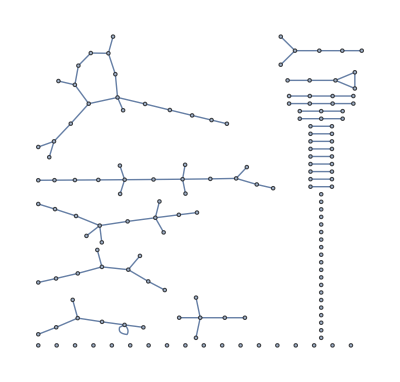

Symmetric: True

Connected: False

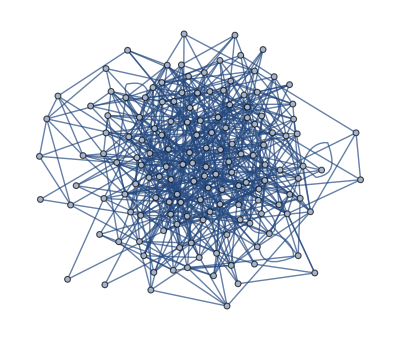

Symmetric: True

Connected: True

```mathematica
test = generateAGraph[150,0.01];
graph = AdjacencyGraph[test]
Print["Symmetric: ", SymmetricMatrixQ[test]]
Print["Connected: ", ConnectedGraphQ[graph]]

test2 = generateAGraph[150,0.05];
graphN = AdjacencyGraph[test2]
Print["Symmetric: ", SymmetricMatrixQ[test2]]
Print["Connected: ", ConnectedGraphQ[graphN]]
```

## Part 2

The followowing function accepts arguments n, p, and m and generates m random graphs using the generateAGraph function written above. This returns the fraction of graphs which are connected, which is thus the probability that a randomly generated graph with the given parameters is connected.

```mathematica
findProbConnected[n_, p_, m_]:= 
Module[{iter = 0,connCount = 0, curGraph},
While[(iter<m),
curGraph = AdjacencyGraph[generateAGraph[n,p]];
If[ConnectedGraphQ[curGraph], connCount = connCount+1, connCount=connCount];
iter=iter + 1;
];
N[connCount/m, 3]
]
```

## Part 3

The following plot displays that there is a clear threshold value of p for every n at which graphs go from unlikely to be connected to being very connected. Lighter values indicate a high probability of connected, while darker values indicate a low probability. For the plot, I used a range of n (size of adjacency matrix is n*n) from 50 to 150 and values of p that are half of the threshold of n = 150 (since this is the minimum threshold) to the threshold of n = 50 (since this is the maximum threshold). The threshold was calculated using the formula p*(n) = (log n)/n. The clear transition in the graph from dark to light values allows us to visualize the “phase transition” from unconnected to connected graphs based on the changing value of p for that particular n value. This phase transition is along the curve Log[n]/n.

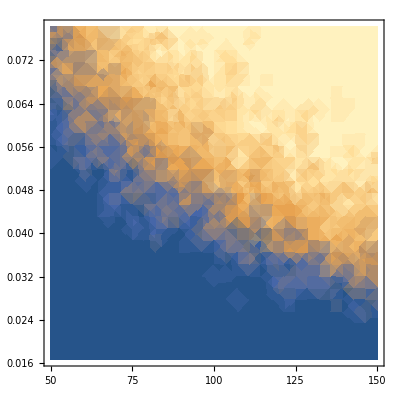

```mathematica
DensityPlot[findProbConnected[n, p, 10], {n, 50, 150}, {p, N[Log[150]/(2*150)], N[(Log[50])/50]}]
```